## Convergence of the scattering coefficients

### Medium parameters

```mathematica
ρI= 997; (*water density*)
ρE= 1275/1000;(*air density*)
cI=1482;(*speed of sound in water*)
cE=34087/100;(*speed of sound in air*)
α =(ρI cI)/(ρE cE);
z=0;
NMax=55;
f=40000; (*ultrasound frequency*)
```

### Scattering Coefficient

```mathematica
DJ[l_,x_]=D[SphericalBesselJ[l,x],x];
DH[l_,x_]=D[SphericalHankelH1[l,x],x];
```

```mathematica
Cfunc[l_,ke_,ki_,a_,α_]:=(α DJ[l,ke a]SphericalBesselJ[l,ki a]-DJ[l,ki a]SphericalBesselJ[l,ke a])/(DJ[l,ki a]SphericalHankelH1[l,ke a]-α DH[l,ke a] SphericalBesselJ[l,ki a]);
```

### Calculations

```mathematica
a1=14 10^(-5);
a2=14 10^(-4);
a3=14 10^(-3);
```

```mathematica
kke=2π f /cE;
kki=2π f /cI;
```

```mathematica
dadosA1=ParallelTable[Log[Abs[Cfunc[ll,kke,kki,a1,α]]],{ll,1,NMax,1}];
dadosA2=ParallelTable[Log[Abs[Cfunc[ll,kke,kki,a2,α]]],{ll,1,NMax,1}];
dadosA3=ParallelTable[Log[Abs[Cfunc[ll,kke,kki,a3,α]]],{ll,1,NMax,1}];
```

### Plot

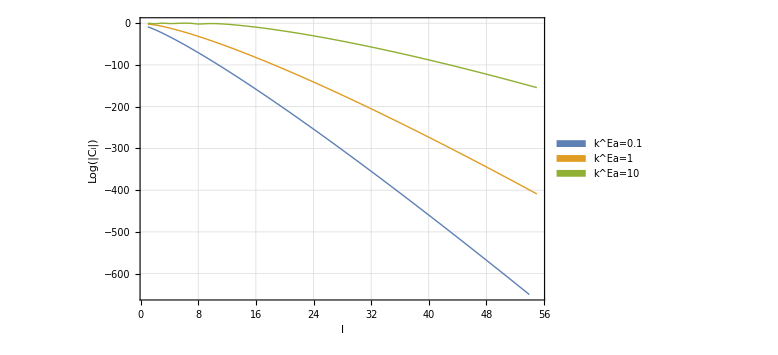

```mathematica
AllFig=ListLinePlot[{dadosA1,dadosA2,dadosA3},PlotRange->{All,{10,-650}},ImageSize->Large,LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],PlotStyle->Thick,FrameStyle->LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],InterpolationOrder->2,PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,Frame->True,ColorFunctionScaling->True,FrameLabel->{"l","Log(|C_l|)"},PlotLegends->Placed[SwatchLegend[Automatic,{Style["k^Ea=0.1",FontFamily->"Helvetica",Black,20],Style["k^Ea=1",FontFamily->"Helvetica",Black,20],Style["k^Ea=10",FontFamily->"Helvetica",Black,20]}],{Right,Bottom}],Epilog->Inset[ListLinePlot[{dadosA1,dadosA2,dadosA3},Background->White,PlotRange->{{1,10},{1,-20}},ImageSize->200,LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->10],PlotStyle->Thick,FrameStyle->LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->10],InterpolationOrder->2,PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,Frame->True,ColorFunctionScaling->True,FrameLabel->{"l","Log(|C_l|)"}],{13,-500}]]
```

### Save Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/antonio/Dropbox/_Papers/[Matheus] Paper 1/Figuras paper

```mathematica
Export["Convergence.png",AllFig,ImageResolution->500]
```

Convergence.png

```mathematica
Export["Convergence.tiff",AllFig,ImageSize->800,ImageResolution->300,"ImageEncoding"->"LZW"]
```

Convergence.tiff